# Initialisation

```mathematica
Subscript[Y, ℓ_,m_][θ_,ϕ_]=SphericalHarmonicY[ℓ,m,θ,ϕ];
```

```mathematica
Subscript[Y, ℓ_][θ_]=SphericalHarmonicY[ℓ,0,θ,ϕ];
```

```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,xcolor,bm,mhchem}","\\definecolor{darkgreen}{RGB}{0, 180, 0}","\\definecolor{darkcyan}{RGB}{0, 180, 180}","\\definecolor{darkmagenta}{RGB}{180,0, 180}"}];
```

# Radius of convergence

```mathematica
Subscript[ψ, i_][θ_]=Subscript[Y, i][θ];
```

```mathematica
Subscript[ϕ, i_]=Subscript[ψ, i][θ1]Subscript[ψ, i][θ2];
```

```mathematica
Subscript[P, l_][θ_]=(√(2l+1))/(4 π) LegendreP[l,Cos[θ]];
```

```mathematica
Subscript[ϵ, l_]=(l (l+1))/(2 R^2) +2/R-1/((2l+1)R);
```

```mathematica
DiagonalMatrix[Table[2 Subscript[ϵ, l],{l,0,8}]];
```

```mathematica
HnRMP[R_]=({{2/R, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 2 (1/R^2+5/(3 R)), 0, 0, 0, 0, 0, 0, 0}, {0, 0, 2 (3/R^2+9/(5 R)), 0, 0, 0, 0, 0, 0}, {0, 0, 0, 2 (6/R^2+13/(7 R)), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 2 (10/R^2+17/(9 R)), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 2 (15/R^2+21/(11 R)), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 2 (21/R^2+25/(13 R)), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 2 (28/R^2+29/(15 R)), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 2 (36/R^2+33/(17 R))}});
```

```mathematica
T[R_]=1/R^2 Table[KroneckerDelta[i,j]i(i+1),{i,0,8},{j,0,8}];
```

```mathematica
({{0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 2/R^2, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 6/R^2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 12/R^2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 20/R^2, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 30/R^2, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 42/R^2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 56/R^2, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 72/R^2}})
```

```mathematica
vsh[i_,j_,n_]:=1/R  ∑_(l=0)^(2n) (2i+1)(2j+1)ThreeJSymbol[{i,0},{j,0},{l,0}]^4
```

```mathematica
Table[vsh[i,j,i+j],{i,0,8},{j,0,8}]//N
```

```mathematica
Vsh[R_]={{1/R,0.3333333333333333/R,0.2/R,0.14285714285714285/R,0.1111111111111111/R,0.09090909090909091/R,0.07692307692307693/R,0.06666666666666667/R,0.058823529411764705/R},{0.3333333333333333/R,1.16/R,0.3768707482993197/R,0.23894179894179896/R,0.17771406083094396/R,0.14227083457852688/R,0.11891502436956983/R,0.10227882311991975/R,0.08979197219053826/R},{0.2/R,0.3768707482993197/R,1.163265306122449/R,0.3735274826183917/R,0.2394342476260558/R,0.18040103974169908/R,0.146121949770896/R,0.12336704694085163/R,0.10701846146841107/R},{0.14285714285714285/R,0.23894179894179896/R,0.3735274826183917/R,1.1585046810221635/R,0.36821375982215143/R,0.23639936203151535/R,0.1789388409525929/R,0.1457035485478321/R,0.123649435931834/R},{0.1111111111111111/R,0.17771406083094396/R,0.2394342476260558/R,0.36821375982215143/R,1.1538451523898603/R,0.36372465712226587/R,0.23326087447106705/R,0.17682041129967005/R,0.14432821252077524/R},{0.09090909090909091/R,0.14227083457852688/R,0.18040103974169908/R,0.23639936203151535/R,0.36372465712226587/R,1.150007604086675/R,0.36012786983290884/R,0.230517596686319/R,0.17475900884511636/R},{0.07692307692307693/R,0.11891502436956983/R,0.146121949770896/R,0.1789388409525929/R,0.23326087447106705/R,0.36012786983290884/R,1.1469018642211581/R,0.35723120605820047/R,0.2281924994972908/R},{0.06666666666666667/R,0.10227882311991975/R,0.12336704694085163/R,0.1457035485478321/R,0.17682041129967005/R,0.230517596686319/R,0.35723120605820047/R,1.1443650135634595/R,0.35486187367716066/R},{0.058823529411764705/R,0.08979197219053826/R,0.10701846146841107/R,0.123649435931834/R,0.14432821252077524/R,0.17475900884511636/R,0.2281924994972908/R,0.35486187367716066/R,1.1422625061276128/R}};
```

```mathematica
Table[(8 π^2)/R∫_0^π Subscript[P, l][θ] 1/(2Sin[θ/2])Subscript[P, m][θ]Sin[θ]ⅆθ,{l,0,8},{m,0,8}]//N
```

```mathematica
Vcsf[R_]={{1/R,0.5773502691896258/R,0.4472135954999579/R,0.3779644730092272/R,0.3333333333333333/R,0.30151134457776363/R,0.2773500981126146/R,0.2581988897471611/R,0.24253562503633297/R},{0.5773502691896258/R,1.4/R,0.848367780597815/R,0.6837493894061095/R,0.592346380077668/R,0.5311600271468729/R,0.48620730337181/R,0.45126077735968606/R,0.4230319832800408/R},{0.4472135954999579/R,0.848367780597815/R,1.5714285714285714/R,0.9885743706824466/R,0.8114774831432803/R,0.7117377302633934/R,0.6440520175728418/R,0.5936999228322687/R,0.5541199346189097/R},{0.3779644730092272/R,0.6837493894061095/R,0.9885743706824466/R,1.6815850815850817/R,1.0845553992409294/R,0.900512006141845/R,0.7959982094351871/R,0.7245684949157892/R,0.6710809207892108/R},{0.3333333333333333/R,0.592346380077668/R,0.8114774831432803/R,1.0845553992409294/R,1.7630017041781747/R,1.1578091708471627/R,0.9692291776523858/R,0.8615000962930917/R,0.787532983589977/R},{0.30151134457776363/R,0.5311600271468729/R,0.7117377302633934/R,0.900512006141845/R,1.1578091708471627/R,1.82765737874097/R,1.2171341675960432/R,1.0253250611469975/R,0.9152400219292804/R},{0.2773500981126146/R,0.48620730337181/R,0.6440520175728418/R,0.7959982094351871/R,0.9692291776523858/R,1.2171341675960432/R,1.8813088755369007/R,1.2670212868739044/R,1.072783723443656/R},{0.2581988897471611/R,0.45126077735968606/R,0.5936999228322687/R,0.7245684949157892/R,0.8615000962930917/R,1.0253250611469975/R,1.2670212868739044/R,1.9271727209854121/R,1.3100807176325626/R},{0.24253562503633297/R,0.4230319832800408/R,0.5541199346189097/R,0.6710809207892108/R,0.787532983589977/R,0.9152400219292804/R,1.072783723443656/R,1.3100807176325626/R,1.9672311134494134/R}};
```

```mathematica
HMPsh[λ_,R_,n_]:=Take[HnRMP[R]+λ (T [R]+ Vsh[R]-HnRMP[R]),n,n]//N;
HMPcsf[λ_,R_,n_]:=Take[HnRMP[R]+λ (T[R]+Vcsf[R]-HnRMP[R]),n,n]//N;
```

```mathematica
HWCEsh[λ_,R_,n_]:=Take[T [R]+ λ Vsh[R],n,n];
HWCEcsf[λ_,R_,n_]:=Take[T[R]+λ Vcsf[R],n,n];
```

```mathematica
HSCEsh[λ_,R_,n_]:=Take[λ T[R]+Vsh[R],n,n];
HSCEcsf[λ_,R_,n_]:=Take[λ T[R]+Vcsf[R],n,n];
```

```mathematica
HENsh[λ_,R_,n_]:=Take[DiagonalMatrix[Diagonal[T[R]+Vsh[R]]]+λ (T[R]+Vsh[R]-DiagonalMatrix[Diagonal[T[R]+Vsh[R]]]),n,n];
HENcsf[λ_,R_,n_]:=Take[DiagonalMatrix[Diagonal[T[R]+Vcsf[R]]]+λ (T[R]+Vcsf[R]-DiagonalMatrix[Diagonal[T[R]+Vcsf[R]]]),n,n];
```

```mathematica
Rcv[R_,H_,n_]:=Module[{P,dPdϵ,EP,λEP},
P[λ_,ϵ_]:=CharacteristicPolynomial[H[λ,R,n],ϵ];
dPdϵ[λ_,ϵ_]:=D[P[λ,ϵ],ϵ];
EP=NSolve[{P[λ,ϵ]==0,dPdϵ[λ,ϵ]==0},{ϵ,λ},WorkingPrecision->30];
{λEP=λ/.EP};
Abs[λEP]//Sort//First]
```

```mathematica
DomSing[R_,H_,n_]:=Module[{P,dPdϵ,EP,λEP},
P[λ_,ϵ_]:=CharacteristicPolynomial[H[λ,R,n],ϵ];
dPdϵ[λ_,ϵ_]:=D[P[λ,ϵ],ϵ];
EP=NSolve[{P[λ,ϵ]==0,dPdϵ[λ,ϵ]==0},{ϵ,λ},WorkingPrecision->30];
{λEP=λ/.EP};
SortBy[λEP,Abs,NumericalOrder]//First]
```

```mathematica
Show[LogLinearPlot[{Rcv[R,HMPsh,2],Rcv[R,HWCEsh,2],Rcv[R,HSCEsh,2],Rcv[R,HENsh,2]},{R,0.5,100},PlotRange->{{0.5,100},{0,6.25}},PlotTheme->"Scientific",FrameStyle->Directive[Thick,16],FrameLabel->{MaTeX["R",Magnification->1.5],MaTeX["R_{\\text{CV}}",Magnification->1.5]},PlotLegends->Placed[{MaTeX["\\text{MP}",Magnification->1.5],MaTeX["\\text{WCE}",Magnification->1.5],MaTeX["\\text{SCE}",Magnification->1.5],MaTeX["\\text{EN}",Magnification->1.5]},{Top,Center}]],LogLinearPlot[1,{R,0.5,500},PlotStyle->{Black,Dotted}],ImageSize->Large]
```

NSolve::precw: The precision of the argument function ({58.6505-18.6638 ϵ+1. ϵ^2-46.7082 λ+6.34598 ϵ λ+8.2471 λ^2,-18.6638+2. ϵ+6.34598 λ}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({0.-7.99827 ϵ+1. ϵ^2+15.9948 λ-4.31953 ϵ λ+4.19465 λ^2,-7.99827+2. ϵ-4.31953 λ}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({4.19465-4.31953 ϵ+1. ϵ^2+15.9948 λ-7.99827 ϵ λ,-4.31953+2. ϵ-7.99827 λ}) is less than WorkingPrecision (30).

General::stop: Further output of NSolve::precw will be suppressed during this calculation.

-Graphics-

```mathematica
Show[LogLinearPlot[{Rcv[R,HMPcsf,2],Rcv[R,HWCEcsf,2],Rcv[R,HSCEcsf,2],Rcv[R,HENcsf,2]},{R,0.5,100},PlotRange->{{0.5,50},{0,5}},PlotTheme->"Scientific",FrameStyle->Directive[Thick,16],FrameLabel->{MaTeX["R",Magnification->1.5],MaTeX["R_{\\text{CV}}",Magnification->1.5]},PlotLegends->Placed[{MaTeX["\\text{MP}",Magnification->1.5],MaTeX["\\text{WCE}",Magnification->1.5],MaTeX["\\text{SCE}",Magnification->1.5],MaTeX["\\text{EN}",Magnification->1.5]},{Top,Center}]],LogLinearPlot[1,{R,0.5,500},PlotStyle->{Black,Dotted}],ImageSize->Large]
```

NSolve::precw: The precision of the argument function ({58.6505-18.6638 ϵ+1. ϵ^2-44.7886 λ+5.86603 ϵ λ+6.39861 λ^2,-18.6638+2. ϵ+5.86603 λ}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({0.-7.99827 ϵ+1. ϵ^2+15.9948 λ-4.79948 ϵ λ+4.26574 λ^2,-7.99827+2. ϵ-4.79948 λ}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({4.26574-4.79948 ϵ+1. ϵ^2+15.9948 λ-7.99827 ϵ λ,-4.79948+2. ϵ-7.99827 λ}) is less than WorkingPrecision (30).

General::stop: Further output of NSolve::precw will be suppressed during this calculation.

-Graphics-

```mathematica
Show[LogLinearPlot[{Rcv[R,HMPcsf,3],Rcv[R,HWCEcsf,3],Rcv[R,HSCEcsf,3],Rcv[R,HENcsf,3]},{R,0.5,100},PlotRange->{{0.5,100},{0,5}},PlotTheme->"Scientific",FrameStyle->Directive[Thick,16],PlotLegends->Placed[{MaTeX["\\text{MP}",Magnification->1.5],MaTeX["\\text{WCE}",Magnification->1.5],MaTeX["\\text{SCE}",Magnification->1.5],MaTeX["\\text{EN}",Magnification->1.5]},{Top,Center}],FrameLabel->{MaTeX["R",Magnification->1.5],MaTeX["R_{\\text{CV}}",Magnification->1.5]}],LogLinearPlot[1,{R,0.5,500},PlotStyle->{Black,Dotted}],ImageSize->Large]
```

NSolve::precw: The precision of the argument function ({1829.55-640.849 ϵ+49.8578 ϵ^2-1. ϵ^3-1635.06 λ+303.487 ϵ λ-9.92274 ϵ^2 λ+358.052 λ^2-26.5173 ϵ λ^2-13.6054 λ^3,-640.849+99.7156 ϵ-3. ϵ^2+303.487 λ-19.8455 ϵ λ-26.5173 λ^2}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({0.-191.917 ϵ+31.9931 ϵ^2-1. ϵ^3+383.792 λ-156.292 ϵ λ+7.942 ϵ^2 λ+146.222 λ^2-15.6701 ϵ λ^2+8.91357 λ^3,-191.917+63.9861 ϵ-3. ϵ^2-156.292 λ+15.884 ϵ λ-15.6701 λ^2}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({8.91357-15.6701 ϵ+7.942 ϵ^2-1. ϵ^3+146.222 λ-156.292 ϵ λ+31.9931 ϵ^2 λ+383.792 λ^2-191.917 ϵ λ^2,-15.6701+15.884 ϵ-3. ϵ^2-156.292 λ+63.9861 ϵ λ-191.917 λ^2}) is less than WorkingPrecision (30).

General::stop: Further output of NSolve::precw will be suppressed during this calculation.

-Graphics-

NSolve::precw: The precision of the argument function ({58.6505-18.6638 ϵ+1. ϵ^2-44.7886 λ+5.86603 ϵ λ+6.39861 λ^2,-18.6638+2. ϵ+5.86603 λ}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({1829.55-640.849 ϵ+49.8578 ϵ^2-1. ϵ^3-1635.06 λ+303.487 ϵ λ-9.92274 ϵ^2 λ+358.052 λ^2-26.5173 ϵ λ^2-13.6054 λ^3,-640.849+99.7156 ϵ-3. ϵ^2+303.487 λ-19.8455 ϵ λ-26.5173 λ^2}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({101389.-37343.7 ϵ+3403.84 ϵ^2-105.275 ϵ^3+1. ϵ^4-98048. λ+21058.6 ϵ λ-1056.05 ϵ^2 λ+13.9877 ϵ^3 λ+25764.9 λ^2-2896.29 ϵ λ^2+60.5036 ϵ^2 λ^2-1634.22 λ^3+68.3897 ϵ λ^3-43.6201 λ^4,-37343.7+6807.68 ϵ-315.826 ϵ^2+4. ϵ^3+21058.6 λ-«1»+41.9631 ϵ^2 λ-2896.29 λ^2+121.007 ϵ λ^2+68.3897 λ^3}) is less than WorkingPrecision (30).

General::stop: Further output of NSolve::precw will be suppressed during this calculation.

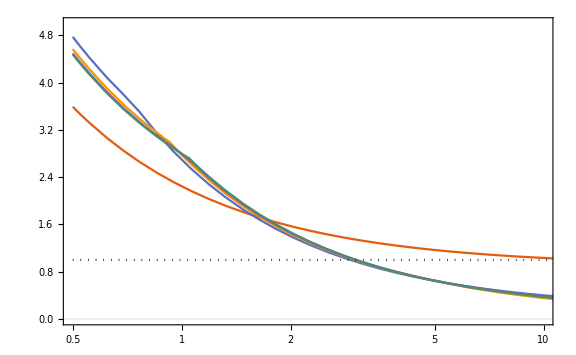

```mathematica
Show[LogLinearPlot[{Rcv[R,HMPcsf,2],Rcv[R,HMPcsf,3],Rcv[R,HMPcsf,4],Rcv[R,HMPcsf,6],Rcv[R,HMPcsf,8]},{R,0.5,100},PlotRange->{{0.5,10},{0,5}},PlotTheme->"Scientific",FrameStyle->Directive[Thick,16],FrameLabel->{MaTeX["R",Magnification->1.5],MaTeX["R_{\\text{CV}}",Magnification->1.5]},PlotLegends->Placed[{MaTeX["K=2",Magnification->1.5],MaTeX["K=3",Magnification->1.5],MaTeX["K=4",Magnification->1.5],MaTeX["K=6",Magnification->1.5],MaTeX["K=8",Magnification->1.5]},{Right,Top}]],LogLinearPlot[1,{R,0.5,500},PlotStyle->{Black,Dotted}],ImageSize->Large]
```

NSolve::precw: The precision of the argument function ({0.-7.99827 ϵ+1. ϵ^2+15.9948 λ-4.79948 ϵ λ+4.26574 λ^2,-7.99827+2. ϵ-4.79948 λ}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({0.-191.917 ϵ+31.9931 ϵ^2-1. ϵ^3+383.792 λ-156.292 ϵ λ+7.942 ϵ^2 λ+146.222 λ^2-15.6701 ϵ λ^2+8.91357 λ^3,-191.917+63.9861 ϵ-3. ϵ^2-156.292 λ+15.884 ϵ λ-15.6701 λ^2}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({0.-9210.02 ϵ+1727.25 ϵ^2-79.9827 ϵ^3+1. ϵ^4+18418. λ-8529.57 ϵ λ+645.012 ϵ^2 λ-11.3048 ϵ^3 λ+8198.13 λ^2-1329.4 ϵ λ^2+36.0283 ϵ^2 λ^2+793.153 λ^3-44.0736 ϵ λ^3+18.419 λ^4,-9210.02+3454.5 ϵ-239.948 ϵ^2+4. ϵ^3-8529.57 λ+1290.02 ϵ λ-33.9144 ϵ^2 λ-1329.4 λ^2+72.0565 ϵ λ^2-44.0736 λ^3}) is less than WorkingPrecision (30).

General::stop: Further output of NSolve::precw will be suppressed during this calculation.

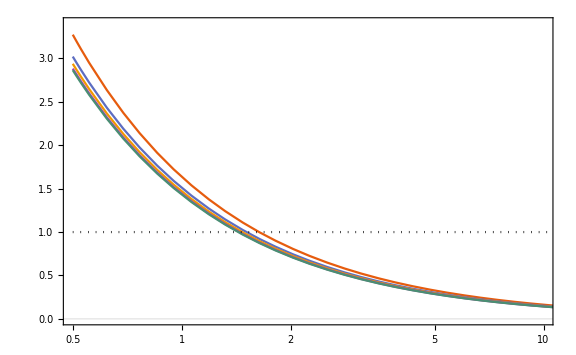

```mathematica
Show[LogLinearPlot[{Rcv[R,HWCEcsf,2],Rcv[R,HWCEcsf,3],Rcv[R,HWCEcsf,4],Rcv[R,HWCEcsf,6],Rcv[R,HWCEcsf,8]},{R,0.5,100},PlotRange->{{0.5,10},{0,3.4}},PlotTheme->"Scientific",FrameStyle->Directive[Thick,16],FrameLabel->{MaTeX["R",Magnification->1.5],MaTeX["R_{\\text{CV}}",Magnification->1.5]},PlotLegends->Placed[{MaTeX["K=2",Magnification->1.5],MaTeX["K=3",Magnification->1.5],MaTeX["K=4",Magnification->1.5],MaTeX["K=6",Magnification->1.5],MaTeX["K=8",Magnification->1.5]},{Right,Top}]],LogLinearPlot[1,{R,0.5,500},PlotStyle->{Black,Dotted}],ImageSize->Large]
```

NSolve::precw: The precision of the argument function ({58.6505-18.6638 ϵ+1. ϵ^2-44.7886 λ+5.86603 ϵ λ+6.39861 λ^2,-18.6638+2. ϵ+5.86603 λ}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({1829.55-640.849 ϵ+49.8578 ϵ^2-1. ϵ^3-1635.06 λ+303.487 ϵ λ-9.92274 ϵ^2 λ+358.052 λ^2-26.5173 ϵ λ^2-13.6054 λ^3,-640.849+99.7156 ϵ-3. ϵ^2+303.487 λ-19.8455 ϵ λ-26.5173 λ^2}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({101389.-37343.7 ϵ+3403.84 ϵ^2-105.275 ϵ^3+1. ϵ^4-98048. λ+21058.6 ϵ λ-1056.05 ϵ^2 λ+13.9877 ϵ^3 λ+25764.9 λ^2-2896.29 ϵ λ^2+60.5036 ϵ^2 λ^2-1634.22 λ^3+68.3897 ϵ λ^3-43.6201 λ^4,-37343.7+6807.68 ϵ-315.826 ϵ^2+4. ϵ^3+21058.6 λ-«1»+41.9631 ϵ^2 λ-2896.29 λ^2+121.007 ϵ λ^2+68.3897 λ^3}) is less than WorkingPrecision (30).

General::stop: Further output of NSolve::precw will be suppressed during this calculation.

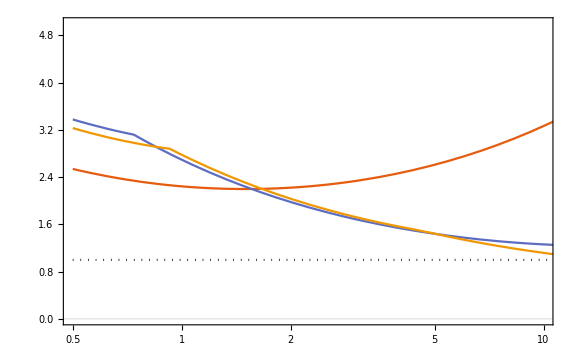

```mathematica
Show[LogLinearPlot[{√R Rcv[R,HMPcsf,2],√R Rcv[R,HMPcsf,3],√R Rcv[R,HMPcsf,4]},{R,0.5,100},PlotRange->{{0.5,10},{0,5}},PlotTheme->"Scientific",FrameStyle->Directive[Thick,16],FrameLabel->{MaTeX["R",Magnification->1.5],MaTeX["R_{\\text{CV}}",Magnification->1.5]},PlotLegends->Placed[{MaTeX["K=2",Magnification->1.5],MaTeX["K=3",Magnification->1.5],MaTeX["K=4",Magnification->1.5],MaTeX["K=6",Magnification->1.5],MaTeX["K=8",Magnification->1.5]},{Right,Top}]],LogLinearPlot[1,{R,0.5,500},PlotStyle->{Black,Dotted}],ImageSize->Large]
```

NSolve::precw: The precision of the argument function ({21.5936-12.7977 ϵ+1. ϵ^2-1.77616×10^-15 λ+8.88178×10^-16 ϵ λ-1.33304 λ^2,-12.7977+2. ϵ+8.88178×10^-16 λ}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({585.992-368.89 ϵ+39.9351 ϵ^2-1. ϵ^3-5.77898×10^-14 λ+3.15623×10^-14 ϵ λ-1.33227×10^-15 ϵ^2 λ-50.5677 λ^2+5.01116 ϵ λ^2+3.50362 λ^3,-368.89+79.8701 ϵ-3. ϵ^2+3.15623×10^-14 λ-2.66454×10^-15 ϵ λ+5.01116 λ^2}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({30092.1-19529.4 ϵ+2419.65 ϵ^2-91.2875 ϵ^3+1. ϵ^4-1.40625×10^-12 λ+6.95669×10^-13 ϵ λ+6.43095×10^-15 ϵ^2 λ-1.33227×10^-15 ϵ^3 λ-2950.04 λ^2+434.069 ϵ λ^2-11.3604 ϵ^2 λ^2+291.886 λ^3-17.735 ϵ λ^3-6.22289 λ^4,-19529.4+4839.31 ϵ-273.862 ϵ^2+4. ϵ^3+«23» λ+«24» ϵ λ-«1»+434.069 λ^2-22.7208 ϵ λ^2-17.735 λ^3}) is less than WorkingPrecision (30).

General::stop: Further output of NSolve::precw will be suppressed during this calculation.

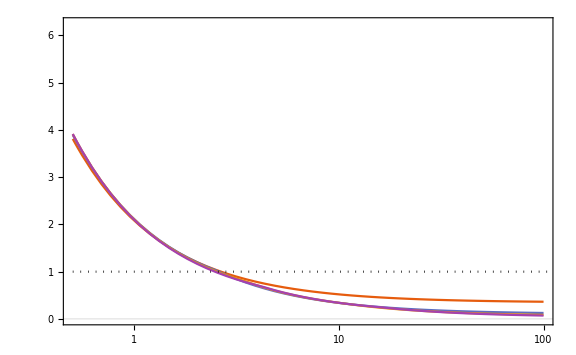

```mathematica
Show[LogLinearPlot[{Rcv[R,HENcsf,2],Rcv[R,HENcsf,3],Rcv[R,HENcsf,4],Rcv[R,HENcsf,5]},{R,0.5,100},PlotRange->{{0.5,100},{0,6.25}},PlotTheme->"Scientific",FrameStyle->Directive[Thick,16],FrameLabel->{MaTeX["R",Magnification->1.5],MaTeX["R_{\\text{CV}}",Magnification->1.5]},PlotLegends->Placed[{MaTeX["2",Magnification->1.5],MaTeX["3",Magnification->1.5],MaTeX["4",Magnification->1.5],MaTeX["5",Magnification->1.5]},{Right,Top}]],LogLinearPlot[1,{R,0.5,500},PlotStyle->{Black,Dotted}],ImageSize->Large]
```

NSolve::precw: The precision of the argument function ({20.6338-12.3178 ϵ+1. ϵ^2+1.77616×10^-15 λ-8.88178×10^-16 ϵ λ-0.444348 λ^2,-12.3178+2. ϵ-8.88178×10^-16 λ}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({543.104-344.852 ϵ+38.6389 ϵ^2-1. ϵ^3+6.50771×10^-14 λ-3.60944×10^-14 ϵ λ+1.77636×10^-15 ϵ^2 λ-14.4821 λ^2+1.17232 ϵ λ^2+0.401865 λ^3,-344.852+77.2778 ϵ-3. ϵ^2-3.60944×10^-14 λ+3.55271×10^-15 ϵ λ+1.17232 λ^2}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({27321.6-17891.3 ϵ+2288.63 ϵ^2-88.9453 ϵ^3+1. ϵ^4+3.27379×10^-12 λ-1.88085×10^-12 ϵ λ+1.25456×10^-13 ϵ^2 λ-1.77636×10^-15 ϵ^3 λ-774.24 λ^2+89.7867 ϵ λ^2-2.04023 ϵ^2 λ^2+27.8438 λ^3-1.29256 ϵ λ^3-0.156218 λ^4,-17891.3+4577.27 ϵ-266.836 ϵ^2+«6»+89.7867 λ^2-4.08045 ϵ λ^2-1.29256 λ^3}) is less than WorkingPrecision (30).

General::stop: Further output of NSolve::precw will be suppressed during this calculation.

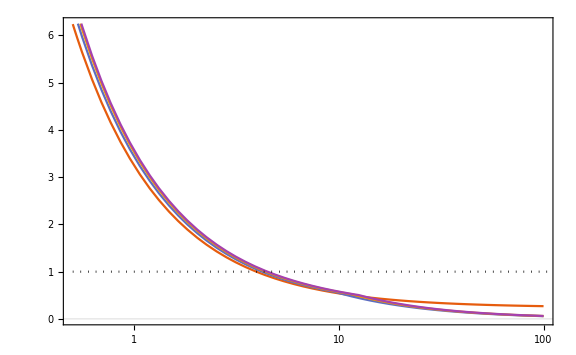

```mathematica
Show[LogLinearPlot[{Rcv[R,HENsh,2],Rcv[R,HENsh,3],Rcv[R,HENsh,4],Rcv[R,HENsh,5]},{R,0.5,100},PlotRange->{{0.5,100},{0,6.25}},PlotTheme->"Scientific",FrameStyle->Directive[Thick,16],FrameLabel->{MaTeX["R",Magnification->1.5],MaTeX["R_{\\text{CV}}",Magnification->1.5]},PlotLegends->Placed[{MaTeX["2",Magnification->1.5],MaTeX["3",Magnification->1.5],MaTeX["4",Magnification->1.5],MaTeX["5",Magnification->1.5]},{Right,Top}]],LogLinearPlot[1,{R,0.5,500},PlotStyle->{Black,Dotted}],ImageSize->Large]
```

NSolve::precw: The precision of the argument function ({58.6505-18.6638 ϵ+1. ϵ^2-46.7082 λ+6.34598 ϵ λ+8.2471 λ^2,-18.6638+2. ϵ+6.34598 λ}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({58.6505-18.6638 ϵ+1. ϵ^2-44.7886 λ+5.86603 ϵ λ+6.39861 λ^2,-18.6638+2. ϵ+5.86603 λ}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({0.-7.99827 ϵ+1. ϵ^2+15.9948 λ-4.31953 ϵ λ+4.19465 λ^2,-7.99827+2. ϵ-4.31953 λ}) is less than WorkingPrecision (30).

General::stop: Further output of NSolve::precw will be suppressed during this calculation.

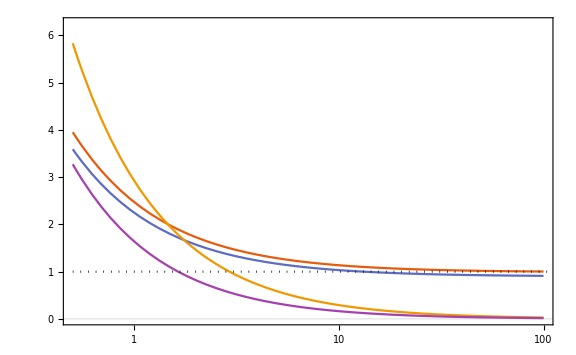

```mathematica
Show[LogLinearPlot[{Rcv[R,HMPsh,2],Rcv[R,HMPcsf,2],Rcv[R,HWCEsh,2],Rcv[R,HWCEcsf,2]},{R,0.5,100},PlotRange->{{0.5,100},{0,6.25}},PlotTheme->"Scientific",FrameStyle->Directive[Thick,16],FrameLabel->{MaTeX["R",Magnification->1.5],MaTeX["R_{\\text{CV}}",Magnification->1.5]},PlotLegends->Placed[{MaTeX["\\text{MP SH}",Magnification->1.5],MaTeX["\\text{MP CSF}",Magnification->1.5],MaTeX["\\text{WCE SH}",Magnification->1.5],MaTeX["\\text{WCE CSF}",Magnification->1.5]},{Right,Top}]],LogLinearPlot[1,{R,0.5,500},PlotStyle->{Black,Dotted}],ImageSize->Large]
```

NSolve::precw: The precision of the argument function ({1829.55-640.849 ϵ+49.8578 ϵ^2-1. ϵ^3-1742.82 λ+335.612 ϵ λ-11.2189 ϵ^2 λ+480.249 λ^2-38.4427 ϵ λ^2-37.9547 λ^3,-640.849+99.7156 ϵ-3. ϵ^2+335.612 λ-22.4378 ϵ λ-38.4427 λ^2}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({1829.55-640.849 ϵ+49.8578 ϵ^2-1. ϵ^3-1635.06 λ+303.487 ϵ λ-9.92274 ϵ^2 λ+358.052 λ^2-26.5173 ϵ λ^2-13.6054 λ^3,-640.849+99.7156 ϵ-3. ϵ^2+303.487 λ-19.8455 ϵ λ-26.5173 λ^2}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({0.-191.917 ϵ+31.9931 ϵ^2-1. ϵ^3+383.792 λ-138.247 ϵ λ+6.64581 ϵ^2 λ+136.579 λ^2-13.5151 ϵ λ^2+8.65282 λ^3,-191.917+63.9861 ϵ-3. ϵ^2-138.247 λ+13.2916 ϵ λ-13.5151 λ^2}) is less than WorkingPrecision (30).

General::stop: Further output of NSolve::precw will be suppressed during this calculation.

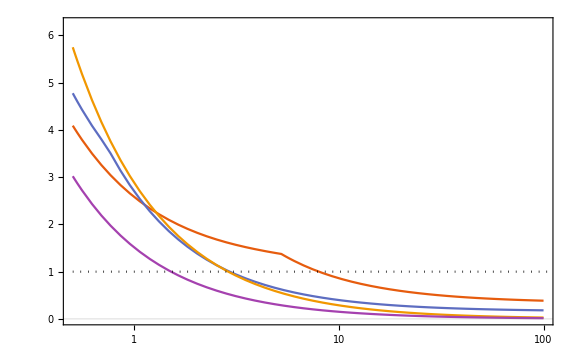

```mathematica
Show[LogLinearPlot[{Rcv[R,HMPsh,3],Rcv[R,HMPcsf,3],Rcv[R,HWCEsh,3],Rcv[R,HWCEcsf,3]},{R,0.5,100},PlotRange->{{0.5,100},{0,6.25}},PlotTheme->"Scientific",FrameStyle->Directive[Thick,16],FrameLabel->{MaTeX["R",Magnification->1.5],MaTeX["R_{\\text{CV}}",Magnification->1.5]},PlotLegends->Placed[{MaTeX["\\text{MP SH}",Magnification->1.5],MaTeX["\\text{MP CSF}",Magnification->1.5],MaTeX["\\text{WCE SH}",Magnification->1.5],MaTeX["\\text{WCE CSF}",Magnification->1.5]},{Right,Top}]],LogLinearPlot[1,{R,0.5,500},PlotStyle->{Black,Dotted}],ImageSize->Large]
```

NSolve::precw: The precision of the argument function ({101389.-37343.7 ϵ+3403.84 ϵ^2-105.275 ϵ^3+1. ϵ^4-105933. λ+23617. ϵ λ-1212.16 ϵ^2 λ+16.3299 ϵ^3 λ+35423.1 λ^2-4303.77 ϵ λ^2+94.9148 ϵ^2 λ^2-4485.92 λ^3+227.683 ϵ λ^3+182.323 λ^4,-37343.7+6807.68 ϵ-315.826 ϵ^2+4. ϵ^3+23617. λ-«19» «1»«1»λ+48.9898 ϵ^2 λ-4303.77 λ^2+189.83 ϵ λ^2+227.683 λ^3}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({101389.-37343.7 ϵ+3403.84 ϵ^2-105.275 ϵ^3+1. ϵ^4-98048. λ+21058.6 ϵ λ-1056.05 ϵ^2 λ+13.9877 ϵ^3 λ+25764.9 λ^2-2896.29 ϵ λ^2+60.5036 ϵ^2 λ^2-1634.22 λ^3+68.3897 ϵ λ^3-43.6201 λ^4,-37343.7+6807.68 ϵ-315.826 ϵ^2+4. ϵ^3+21058.6 λ-«1»+41.9631 ϵ^2 λ-2896.29 λ^2+121.007 ϵ λ^2+68.3897 λ^3}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({0.-9210.02 ϵ+1727.25 ϵ^2-79.9827 ϵ^3+1. ϵ^4+18418. λ-7462.85 ϵ λ+531.297 ϵ^2 λ-8.96257 ϵ^3 λ+7427.85 λ^2-1092.9 ϵ λ^2+28.0439 ϵ^2 λ^2+711.456 λ^3-37.0777 ϵ λ^3+17.6945 λ^4,-9210.02+3454.5 ϵ-239.948 ϵ^2+4. ϵ^3-7462.85 λ+1062.59 ϵ λ-26.8877 ϵ^2 λ-1092.9 λ^2+56.0879 ϵ λ^2-37.0777 λ^3}) is less than WorkingPrecision (30).

General::stop: Further output of NSolve::precw will be suppressed during this calculation.

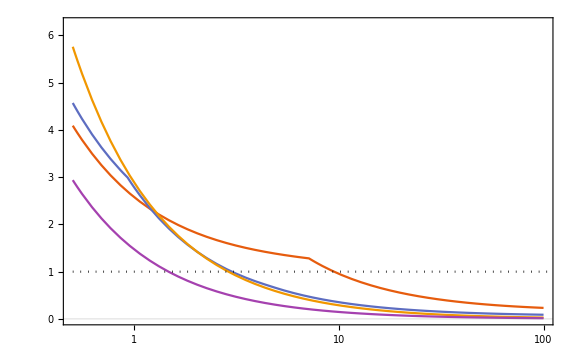

```mathematica
Show[LogLinearPlot[{Rcv[R,HMPsh,4],Rcv[R,HMPcsf,4],Rcv[R,HWCEsh,4],Rcv[R,HWCEcsf,4]},{R,0.5,100},PlotRange->{{0.5,100},{0,6.25}},PlotTheme->"Scientific",FrameStyle->Directive[Thick,16],FrameLabel->{MaTeX["R",Magnification->1.5],MaTeX["R_{\\text{CV}}",Magnification->1.5]},PlotLegends->Placed[{MaTeX["\\text{MP SH}",Magnification->1.5],MaTeX["\\text{MP CSF}",Magnification->1.5],MaTeX["\\text{WCE SH}",Magnification->1.5],MaTeX["\\text{WCE CSF}",Magnification->1.5]},{Right,Top}]],LogLinearPlot[1,{R,0.5,500},PlotStyle->{Black,Dotted}],ImageSize->Large]
```

```mathematica
Table[N[DomSing[R,HMPcsf,8],3],{R,{0.1,1,2,3,5,10,100,1000}}]
```

NSolve::precw: The precision of the argument function («1») is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({(0.+0.451261 λ) (0.-5.01935×10^6 λ+«37»+8294.76 λ^6-466.148 ϵ λ^6-201.738 λ^7)+«10»+(59.8667-1. ϵ-«19» λ) («1»),«1»}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({(0.+0.22563 λ) (0.-2912.18 λ+«37»+38.1863 λ^6-7.28356 ϵ λ^6-1.57608 λ^7)+«10»+(15.9333-1. ϵ-«19» λ) («1»),«1»}) is less than WorkingPrecision (30).

General::stop: Further output of NSolve::precw will be suppressed during this calculation.

{14.1-11. ⅈ,2.38-1.5 ⅈ,-0.67-1.3 ⅈ,-0.48-0.885 ⅈ,-0.33-0.554 ⅈ,-0.22-0.306 ⅈ,0.026-0.0492 ⅈ,0.0046-0.0118 ⅈ}

```mathematica
Table[N[DomSing[R,HWCEcsf,8],3],{R,{0.1,1,2,3,5,10,100,1000}}]
```

NSolve::precw: The precision of the argument function ({«1»,«1»}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({(0.+1.02533 λ) (0.+124023. ϵ λ-102172. ϵ^2 λ+«36»+1.57527 ϵ λ^6-0.163894 λ^7)+«1»+«9»+(56-1. ϵ+1.92717 λ) («1»),«1»}) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function («1») is less than WorkingPrecision (30).

General::stop: Further output of NSolve::precw will be suppressed during this calculation.

{-9.6-10.7 ⅈ,-0.96-1.07 ⅈ,-0.48-0.534 ⅈ,-0.32-0.356 ⅈ,-0.19-0.213 ⅈ,-0.096-0.107 ⅈ,-0.0096-0.0107 ⅈ,-0.00096-0.00107 ⅈ}